```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/nathan/olin/fall2016/ThinkBayes2/code

```mathematica
cigsLungsIntensity=Import["cigsLungsIntensity.csv","CSV"];
cigsLungs=Import["cigsLungs.csv","CSV"];
cigsLungsFitted=Import["cigsLungsFitted.csv","CSV"];
```

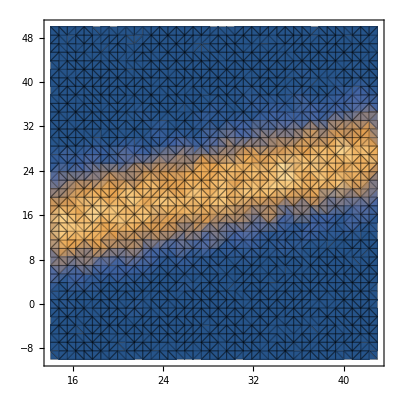

```mathematica
densityPlot=ListDensityPlot[cigsLungsIntensity,Mesh->All]
```

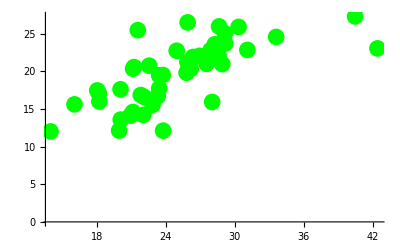

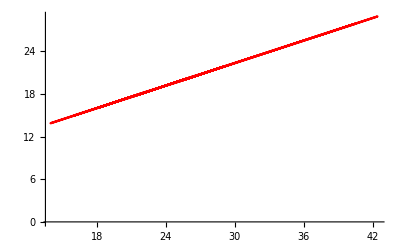

```mathematica
dataPlot=ListPlot[cigsLungs,PlotStyle->Directive[Green,PointSize[.03]]]
fittedLinePlot=ListLinePlot[cigsLungsFitted,PlotStyle->Red]
```

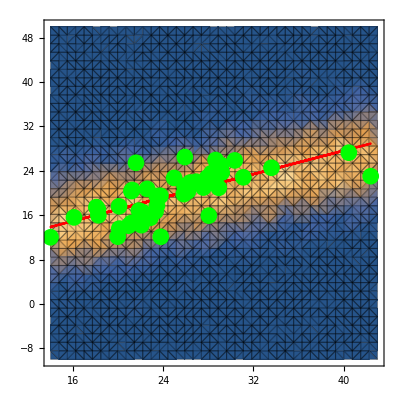

```mathematica
Show[densityPlot,dataPlot,fittedLinePlot]
```

```mathematica
|
```